```mathematica
xDot[x_,r_]:=r x+4x^3 - 9x^5
dxDot[x_,r_]=D[xDot[x,r],x]
```

r+12 x^2-45 x^4

```mathematica
Solve[dxDot[x,r]==0,x]
```

{{x→-(√(2-√(4+5 r)))/(√15)},{x→(√(2-√(4+5 r)))/(√15)},{x→-(√(2+√(4+5 r)))/(√15)},{x→(√(2+√(4+5 r)))/(√15)}}

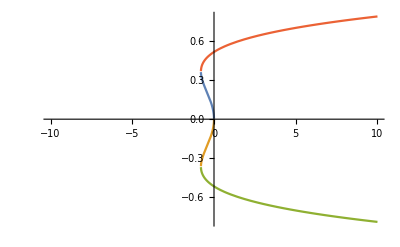

```mathematica
r=.
xRoot1=.; xRoot2=.;xRoot3=.;xRoot4=.;
xRoot1[r_]:= (√(2-√(4+5 r)))/(√15)
xRoot2[r_]:= -xRoot1[r]
xRoot3[r_]:= -(√(2+√(4+5 r)))/(√15)
xRoot4[r_]:= -xRoot3[r]
Plot[{xRoot1[r],xRoot2[r],xRoot3[r],xRoot4[r]},{r,-10,10}]
```